## Scientific Programming 3

Structure of Mathematica

### Numbers

```mathematica
Head/@{3,22/7,3.14,2.34+2.09 ⅈ, π}
```

{Integer,Rational,Real,Complex,Symbol}

```mathematica
FullForm/@{3,22/7,3.14,2.34+2.09 ⅈ, π}
```

{3,Rational[22,7],3.14,Complex[2.34,2.09],Pi}

```mathematica
7==7.0
```

True

```mathematica
7===7.0
```

False

```mathematica
x==7
```

x==7

```mathematica
x===7
```

False

```mathematica
{ⅇ^π,π^ⅇ}//N
```

{23.1407,22.4592}

```mathematica
ⅇ^π> π^ⅇ
```

True

```mathematica
ⅇ^π< π^ⅇ
```

False

```mathematica
IntegerDigits[3569]
```

{3,5,6,9}

```mathematica
FromDigits[%]
```

3569

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
RealDigits[%]
```

{{5,7,7,2,1,5,6,6,4,9,0,1,5,3,2,9},0}

```mathematica
RealDigits[325.23]
```

{{3,2,5,2,3,0,0,0,0,0,0,0,0,0,0,0},3}

```mathematica
RealDigits[N[EulerGamma],2]
```

{{1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,0,1,1,1,1,1,0,1,1,0,1,1,0,0,0,0,1,1,0,0,1},0}

### Precision and Accuracy

```mathematica
e=N[ⅇ]
```

2.71828

```mathematica
FullForm[e]
```

2.71828

```mathematica
x=1.5
```

1.5

```mathematica
FullForm[x]
```

1.5

```mathematica
1.5 π
```

4.71239

```mathematica
N[1.5 π,100]
```

4.71239

```mathematica
N[3/2 π,100]
```

4.712388980384689857693965074919254326295754099062658731462416888461724609429313497942052238013175602

```mathematica
2/3%
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
%==N[π,100]
```

True

```mathematica
x=1.5``100
```

1.5

```mathematica
N[x π,100]==N[3/2 π,100]
```

True

```mathematica
Precision[x]
```

100.176

```mathematica
Accuracy[x]
```

100.

```mathematica
?Precision
```

Precision[x] gives the effective number of digits of precision in the number x.

```mathematica
Precision[3/2]
```

∞

### Solving differential equations

```mathematica
eq[t_]:=y''[t]-1/5(1-y[t]^2)y'[t] + y[t]
```

```mathematica
soln=NDSolve[{eq[t]==0,y[0]==1,y'[0]==0},y,{t,0,30}]
```

{{y→InterpolatingFunction[…]}}

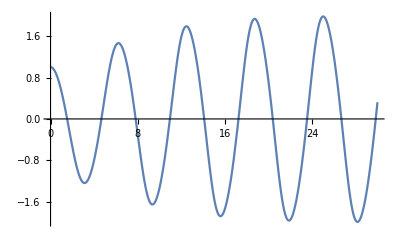

```mathematica
Plot[y[t]/.soln,{t,0,30},
         ImageSize->400]
```

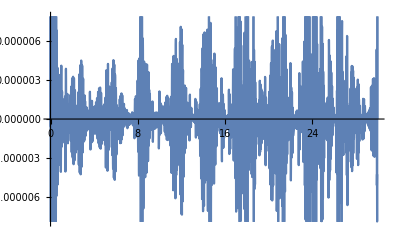

```mathematica
Plot[eq[t]/.soln,{t,0,30},
         ImageSize->400]
```

```mathematica
soln40=
NDSolve[{eq[t]==0,y[0]==1,y'[0]==0},y,{t,0,30},
                WorkingPrecision->40, PrecisionGoal->35]
```

{{y→InterpolatingFunction[{{0, 30.00000000000000000000000000000000000000}}, <>]}}

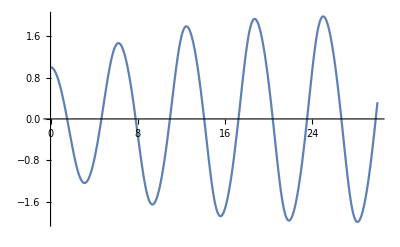

```mathematica
Plot[y[t]/.soln40,{t,0,30},
         ImageSize->400]
```

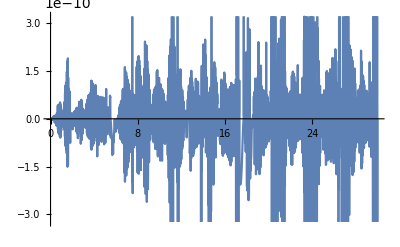

```mathematica
Plot[eq[t]/.soln40,{t,0,30},
         ImageSize->400]
```

```mathematica
Clear[x,f]
```

```mathematica
eq=4 x(x-1) f''[x]+(10 x-4) f'[x]+2 f[x]-(3 (x-3))/(1-x)^(3/2)
```

-(3 (-3+x))/(1-x)^(3/2)+2 f[x]+(-4+10 x) f'[x]+4 (-1+x) x f''[x]

We want a solution f[x] that vanishes at x=0.

```mathematica
fsoln=DSolve[{eq==0,f[0]==0},f,x]⟦1⟧//FullSimplify
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Let us try again, and temporarily drop the condition f[0] = 0.

```mathematica
fsoln=DSolve[eq==0,f,x]⟦1⟧//FullSimplify
```

{f→Function[{x},C[1]/(√(1-x))+(C[2] (Log[1-√(1-x)]-Log[1+√(1-x)]))/(√(1-x))-(3 (√(1-x) Log[1-√(1-x)]+√(1-x) Log[1+√(1-x)]-2 √(1-x) Log[1-x]))/(2 (-1+x))]}

```mathematica
fser=Series[(f/.fsoln)⟦2⟧,{x,0,1}]
```

(C[1]-2 C[2] Log[2]+(3 Log[x])/2+C[2] Log[x])+1/4 (12+2 C[1]+2 C[2]-4 C[2] Log[2]+3 Log[x]+2 C[2] Log[x]) x+O[x]^2

```mathematica
MapAt[Simplify,fser,3]
```

(C[1]-C[2] Log[4]+(3/2+C[2]) Log[x])+1/4 (2 (6+C[1]+C[2]-C[2] Log[4])+(3+2 C[2]) Log[x]) x+O[x]^2

```mathematica
fser/.{C[2]->-3/2, C[1]-> -3Log[2]}
```

(9 x)/4+O[x]^2

```mathematica
F=(f/.fsoln)⟦2⟧/.{C[2]->-3/2, C[1]-> -3Log[2]} //Simplify
```

(3 (Log[1+√(1-x)]-Log[2-2 x]))/(√(1-x))

```mathematica
Series[F,{x,0,2}]
```

(9 x)/4+(75 x^2)/32+O[x]^3

A project to with the periods of a CY manifold

```mathematica
Tpoly[x_,y_]:=x+1/x+y+1/y+x/y+y/x
```

```mathematica
Subscript[T, k_]:=Subscript[T, k]=
Coefficient[
Coefficient[Tpoly[x,y]^k,x,0],
                        y,0]
```

```mathematica
Subscript[α, n_]:= Subscript[α, n]=
If[OddQ[n],2Sum[Binomial[n,k] Subscript[T, n-k] Subscript[T, k],{k,0,(n-1)/2}],2Sum[Binomial[n,k] Subscript[T, n-k] Subscript[T, k],{k,0,n/2-1}]+Binomial[n,n/2] Subscript[T, n/2]^2
       ]
```

```mathematica
Table[Subscript[α, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
Subscript[ϖ, 0]:=Sum[Subscript[α, n] φ^n,{n,0,50}]+O[φ]^51
```

```mathematica
θ[fn_]:=φ D[fn,φ]

θ[fn_,m_]:=Nest[θ,fn,m]
```

```mathematica
θ[φ^n]
```

n φ^n

```mathematica
θ[φ^n,4]
```

n^4 φ^n

```mathematica
Subscript[R, j_,kmax_]:=Sum[Subscript[r, j,k] φ^k,{k,0,kmax}]
```

```mathematica
L[fn_,kmax_]:=Sum[Subscript[R, j,kmax] θ[fn,j],{j,0,4}]
```

```mathematica
With[{kmax=3},
Union[
CoefficientList[
Normal[L[Subscript[ϖ, 0],kmax]],φ]] 
          ]
```

{r_(0,0),r_(0,1),12 r_(0,0)+r_(0,2)+24 r_(1,0)+48 r_(2,0)+96 r_(3,0)+192 r_(4,0),24 r_(0,0)+12 r_(0,1)+r_(0,3)+72 r_(1,0)+24 r_(1,1)+216 r_(2,0)+48 r_(2,1)+648 r_(3,0)+96 r_(3,1)+1944 r_(4,0)+192 r_(4,1),396 r_(0,0)+24 r_(0,1)+12 r_(0,2)+1584 r_(1,0)+72 r_(1,1)+24 r_(1,2)+6336 r_(2,0)+216 r_(2,1)+48 r_(2,2)+25344 r_(3,0)+648 r_(3,1)+96 r_(3,2)+101376 r_(4,0)+1944 r_(4,1)+192 r_(4,2),2160 r_(0,0)+396 r_(0,1)+24 r_(0,2)+12 r_(0,3)+10800 r_(1,0)+1584 r_(1,1)+72 r_(1,2)+24 r_(1,3)+54000 r_(2,0)+6336 r_(2,1)+216 r_(2,2)+48 r_(2,3)+270000 r_(3,0)+25344 r_(3,1)+648 r_(3,2)+96 r_(3,3)+1350000 r_(4,0)+101376 r_(4,1)+1944 r_(4,2)+192 r_(4,3),23160 r_(0,0)+2160 r_(0,1)+396 r_(0,2)+24 r_(0,3)+138960 r_(1,0)+10800 r_(1,1)+1584 r_(1,2)+72 r_(1,3)+833760 r_(2,0)+54000 r_(2,1)+6336 r_(2,2)+216 r_(2,3)+5002560 r_(3,0)+270000 r_(3,1)+25344 r_(3,2)+648 r_(3,3)+30015360 r_(4,0)+1350000 r_(4,1)+101376 r_(4,2)+1944 r_(4,3),186480 r_(0,0)+23160 r_(0,1)+2160 r_(0,2)+396 r_(0,3)+1305360 r_(1,0)+138960 r_(1,1)+10800 r_(1,2)+1584 r_(1,3)+9137520 r_(2,0)+833760 r_(2,1)+54000 r_(2,2)+6336 r_(2,3)+63962640 r_(3,0)+5002560 r_(3,1)+270000 r_(3,2)+25344 r_(3,3)+447738480 r_(4,0)+30015360 r_(4,1)+1350000 r_(4,2)+101376 r_(4,3),1845900 r_(0,0)+186480 r_(0,1)+23160 r_(0,2)+2160 r_(0,3)+14767200 r_(1,0)+1305360 r_(1,1)+138960 r_(1,2)+10800 r_(1,3)+118137600 r_(2,0)+9137520 r_(2,1)+833760 r_(2,2)+54000 r_(2,3)+945100800 r_(3,0)+63962640 r_(3,1)+5002560 r_(3,2)+270000 r_(3,3)+7560806400 r_(4,0)+447738480 r_(4,1)+30015360 r_(4,2)+1350000 r_(4,3),17213280 r_(0,0)+1845900 r_(0,1)+186480 r_(0,2)+23160 r_(0,3)+154919520 r_(1,0)+14767200 r_(1,1)+1305360 r_(1,2)+138960 r_(1,3)+1394275680 r_(2,0)+118137600 r_(2,1)+9137520 r_(2,2)+833760 r_(2,3)+12548481120 r_(3,0)+945100800 r_(3,1)+63962640 r_(3,2)+5002560 r_(3,3)+112936330080 r_(4,0)+7560806400 r_(4,1)+447738480 r_(4,2)+30015360 r_(4,3),171575712 r_(0,0)+17213280 r_(0,1)+1845900 r_(0,2)+186480 r_(0,3)+1715757120 r_(1,0)+154919520 r_(1,1)+14767200 r_(1,2)+1305360 r_(1,3)+17157571200 r_(2,0)+1394275680 r_(2,1)+118137600 r_(2,2)+9137520 r_(2,3)+171575712000 r_(3,0)+12548481120 r_(3,1)+945100800 r_(3,2)+63962640 r_(3,3)+1715757120000 r_(4,0)+112936330080 r_(4,1)+7560806400 r_(4,2)+447738480 r_(4,3),1703560320 r_(0,0)+171575712 r_(0,1)+17213280 r_(0,2)+1845900 r_(0,3)+18739163520 r_(1,0)+1715757120 r_(1,1)+154919520 r_(1,2)+14767200 r_(1,3)+206130798720 r_(2,0)+17157571200 r_(2,1)+1394275680 r_(2,2)+118137600 r_(2,3)+2267438785920 r_(3,0)+171575712000 r_(3,1)+12548481120 r_(3,2)+945100800 r_(3,3)+24941826645120 r_(4,0)+1715757120000 r_(4,1)+112936330080 r_(4,2)+7560806400 r_(4,3),17365421304 r_(0,0)+1703560320 r_(0,1)+171575712 r_(0,2)+17213280 r_(0,3)+208385055648 r_(1,0)+18739163520 r_(1,1)+1715757120 r_(1,2)+154919520 r_(1,3)+2500620667776 r_(2,0)+206130798720 r_(2,1)+17157571200 r_(2,2)+1394275680 r_(2,3)+30007448013312 r_(3,0)+2267438785920 r_(3,1)+171575712000 r_(3,2)+12548481120 r_(3,3)+360089376159744 r_(4,0)+24941826645120 r_(4,1)+1715757120000 r_(4,2)+112936330080 r_(4,3),178323713568 r_(0,0)+17365421304 r_(0,1)+1703560320 r_(0,2)+171575712 r_(0,3)+2318208276384 r_(1,0)+208385055648 r_(1,1)+18739163520 r_(1,2)+1715757120 r_(1,3)+30136707592992 r_(2,0)+2500620667776 r_(2,1)+206130798720 r_(2,2)+17157571200 r_(2,3)+391777198708896 r_(3,0)+30007448013312 r_(3,1)+2267438785920 r_(3,2)+171575712000 r_(3,3)+5093103583215648 r_(4,0)+360089376159744 r_(4,1)+24941826645120 r_(4,2)+1715757120000 r_(4,3),1856554560432 r_(0,0)+178323713568 r_(0,1)+17365421304 r_(0,2)+1703560320 r_(0,3)+25991763846048 r_(1,0)+2318208276384 r_(1,1)+208385055648 r_(1,2)+18739163520 r_(1,3)+363884693844672 r_(2,0)+30136707592992 r_(2,1)+2500620667776 r_(2,2)+206130798720 r_(2,3)+5094385713825408 r_(3,0)+391777198708896 r_(3,1)+30007448013312 r_(3,2)+2267438785920 r_(3,3)+71321399993555712 r_(4,0)+5093103583215648 r_(4,1)+360089376159744 r_(4,2)+24941826645120 r_(4,3),19487791106784 r_(0,0)+1856554560432 r_(0,1)+178323713568 r_(0,2)+17365421304 r_(0,3)+292316866601760 r_(1,0)+25991763846048 r_(1,1)+2318208276384 r_(1,2)+208385055648 r_(1,3)+4384752999026400 r_(2,0)+363884693844672 r_(2,1)+30136707592992 r_(2,2)+2500620667776 r_(2,3)+65771294985396000 r_(3,0)+5094385713825408 r_(3,1)+391777198708896 r_(3,2)+30007448013312 r_(3,3)+986569424780940000 r_(4,0)+71321399993555712 r_(4,1)+5093103583215648 r_(4,2)+360089376159744 r_(4,3),206411964321420 r_(0,0)+19487791106784 r_(0,1)+1856554560432 r_(0,2)+178323713568 r_(0,3)+3302591429142720 r_(1,0)+292316866601760 r_(1,1)+25991763846048 r_(1,2)+2318208276384 r_(1,3)+52841462866283520 r_(2,0)+4384752999026400 r_(2,1)+363884693844672 r_(2,2)+30136707592992 r_(2,3)+845463405860536320 r_(3,0)+65771294985396000 r_(3,1)+5094385713825408 r_(3,2)+391777198708896 r_(3,3)+13527414493768581120 r_(4,0)+986569424780940000 r_(4,1)+71321399993555712 r_(4,2)+5093103583215648 r_(4,3),2201711191213248 r_(0,0)+206411964321420 r_(0,1)+19487791106784 r_(0,2)+1856554560432 r_(0,3)+37429090250625216 r_(1,0)+3302591429142720 r_(1,1)+292316866601760 r_(1,2)+25991763846048 r_(1,3)+636294534260628672 r_(2,0)+52841462866283520 r_(2,1)+4384752999026400 r_(2,2)+363884693844672 r_(2,3)+10817007082430687424 r_(3,0)+845463405860536320 r_(3,1)+65771294985396000 r_(3,2)+5094385713825408 r_(3,3)+183889120401321686208 r_(4,0)+13527414493768581120 r_(4,1)+986569424780940000 r_(4,2)+71321399993555712 r_(4,3),23642813637773616 r_(0,0)+2201711191213248 r_(0,1)+206411964321420 r_(0,2)+19487791106784 r_(0,3)+425570645479925088 r_(1,0)+37429090250625216 r_(1,1)+3302591429142720 r_(1,2)+292316866601760 r_(1,3)+7660271618638651584 r_(2,0)+636294534260628672 r_(2,1)+52841462866283520 r_(2,2)+4384752999026400 r_(2,3)+137884889135495728512 r_(3,0)+10817007082430687424 r_(3,1)+845463405860536320 r_(3,2)+65771294985396000 r_(3,3)+2481928004438923113216 r_(4,0)+183889120401321686208 r_(4,1)+13527414493768581120 r_(4,2)+986569424780940000 r_(4,3),255355132936441824 r_(0,0)+23642813637773616 r_(0,1)+2201711191213248 r_(0,2)+206411964321420 r_(0,3)+4851747525792394656 r_(1,0)+425570645479925088 r_(1,1)+37429090250625216 r_(1,2)+3302591429142720 r_(1,3)+92183202990055498464 r_(2,0)+7660271618638651584 r_(2,1)+636294534260628672 r_(2,2)+52841462866283520 r_(2,3)+1751480856811054470816 r_(3,0)+137884889135495728512 r_(3,1)+10817007082430687424 r_(3,2)+845463405860536320 r_(3,3)+33278136279410034945504 r_(4,0)+2481928004438923113216 r_(4,1)+183889120401321686208 r_(4,2)+13527414493768581120 r_(4,3),2772650461148938656 r_(0,0)+255355132936441824 r_(0,1)+23642813637773616 r_(0,2)+2201711191213248 r_(0,3)+55453009222978773120 r_(1,0)+4851747525792394656 r_(1,1)+425570645479925088 r_(1,2)+37429090250625216 r_(1,3)+1109060184459575462400 r_(2,0)+92183202990055498464 r_(2,1)+7660271618638651584 r_(2,2)+636294534260628672 r_(2,3)+22181203689191509248000 r_(3,0)+1751480856811054470816 r_(3,1)+137884889135495728512 r_(3,2)+10817007082430687424 r_(3,3)+443624073783830184960000 r_(4,0)+33278136279410034945504 r_(4,1)+2481928004438923113216 r_(4,2)+183889120401321686208 r_(4,3),30248675037382538880 r_(0,0)+2772650461148938656 r_(0,1)+255355132936441824 r_(0,2)+23642813637773616 r_(0,3)+635222175785033316480 r_(1,0)+55453009222978773120 r_(1,1)+4851747525792394656 r_(1,2)+425570645479925088 r_(1,3)+13339665691485699646080 r_(2,0)+1109060184459575462400 r_(2,1)+92183202990055498464 r_(2,2)+7660271618638651584 r_(2,3)+280132979521199692567680 r_(3,0)+22181203689191509248000 r_(3,1)+1751480856811054470816 r_(3,2)+137884889135495728512 r_(3,3)+5882792569945193543921280 r_(4,0)+443624073783830184960000 r_(4,1)+33278136279410034945504 r_(4,2)+2481928004438923113216 r_(4,3),331438542846964180992 r_(0,0)+30248675037382538880 r_(0,1)+2772650461148938656 r_(0,2)+255355132936441824 r_(0,3)+7291647942633211981824 r_(1,0)+635222175785033316480 r_(1,1)+55453009222978773120 r_(1,2)+4851747525792394656 r_(1,3)+160416254737930663600128 r_(2,0)+13339665691485699646080 r_(2,1)+1109060184459575462400 r_(2,2)+92183202990055498464 r_(2,3)+3529157604234474599202816 r_(3,0)+280132979521199692567680 r_(3,1)+22181203689191509248000 r_(3,2)+1751480856811054470816 r_(3,3)+77641467293158441182461952 r_(4,0)+5882792569945193543921280 r_(4,1)+443624073783830184960000 r_(4,2)+33278136279410034945504 r_(4,3),3645985314663912489984 r_(0,0)+331438542846964180992 r_(0,1)+30248675037382538880 r_(0,2)+2772650461148938656 r_(0,3)+83857662237269987269632 r_(1,0)+7291647942633211981824 r_(1,1)+635222175785033316480 r_(1,2)+55453009222978773120 r_(1,3)+1928726231457209707201536 r_(2,0)+160416254737930663600128 r_(2,1)+13339665691485699646080 r_(2,2)+1109060184459575462400 r_(2,3)+44360703323515823265635328 r_(3,0)+3529157604234474599202816 r_(3,1)+280132979521199692567680 r_(3,2)+22181203689191509248000 r_(3,3)+1020296176440863935109612544 r_(4,0)+77641467293158441182461952 r_(4,1)+5882792569945193543921280 r_(4,2)+443624073783830184960000 r_(4,3),40253352687777620374776 r_(0,0)+3645985314663912489984 r_(0,1)+331438542846964180992 r_(0,2)+30248675037382538880 r_(0,3)+966080464506662888994624 r_(1,0)+83857662237269987269632 r_(1,1)+7291647942633211981824 r_(1,2)+635222175785033316480 r_(1,3)+23185931148159909335870976 r_(2,0)+1928726231457209707201536 r_(2,1)+160416254737930663600128 r_(2,2)+13339665691485699646080 r_(2,3)+556462347555837824060903424 r_(3,0)+44360703323515823265635328 r_(3,1)+3529157604234474599202816 r_(3,2)+280132979521199692567680 r_(3,3)+13355096341340107777461682176 r_(4,0)+1020296176440863935109612544 r_(4,1)+77641467293158441182461952 r_(4,2)+5882792569945193543921280 r_(4,3),445899348810135736176960 r_(0,0)+40253352687777620374776 r_(0,1)+3645985314663912489984 r_(0,2)+331438542846964180992 r_(0,3)+11147483720253393404424000 r_(1,0)+966080464506662888994624 r_(1,1)+83857662237269987269632 r_(1,2)+7291647942633211981824 r_(1,3)+278687093006334835110600000 r_(2,0)+23185931148159909335870976 r_(2,1)+1928726231457209707201536 r_(2,2)+160416254737930663600128 r_(2,3)+6967177325158370877765000000 r_(3,0)+556462347555837824060903424 r_(3,1)+44360703323515823265635328 r_(3,2)+3529157604234474599202816 r_(3,3)+174179433128959271944125000000 r_(4,0)+13355096341340107777461682176 r_(4,1)+1020296176440863935109612544 r_(4,2)+77641467293158441182461952 r_(4,3),4954599887270237905852800 r_(0,0)+445899348810135736176960 r_(0,1)+40253352687777620374776 r_(0,2)+3645985314663912489984 r_(0,3)+128819597069026185552172800 r_(1,0)+11147483720253393404424000 r_(1,1)+966080464506662888994624 r_(1,2)+83857662237269987269632 r_(1,3)+3349309523794680824356492800 r_(2,0)+278687093006334835110600000 r_(2,1)+23185931148159909335870976 r_(2,2)+1928726231457209707201536 r_(2,3)+87082047618661701433268812800 r_(3,0)+6967177325158370877765000000 r_(3,1)+556462347555837824060903424 r_(3,2)+44360703323515823265635328 r_(3,3)+2264133238085204237264989132800 r_(4,0)+174179433128959271944125000000 r_(4,1)+13355096341340107777461682176 r_(4,2)+1020296176440863935109612544 r_(4,3),55210013720527863783880320 r_(0,0)+4954599887270237905852800 r_(0,1)+445899348810135736176960 r_(0,2)+40253352687777620374776 r_(0,3)+1490670370454252322164768640 r_(1,0)+128819597069026185552172800 r_(1,1)+11147483720253393404424000 r_(1,2)+966080464506662888994624 r_(1,3)+40248100002264812698448753280 r_(2,0)+3349309523794680824356492800 r_(2,1)+278687093006334835110600000 r_(2,2)+23185931148159909335870976 r_(2,3)+1086698700061149942858116338560 r_(3,0)+87082047618661701433268812800 r_(3,1)+6967177325158370877765000000 r_(3,2)+556462347555837824060903424 r_(3,3)+29340864901651048457169141141120 r_(4,0)+2264133238085204237264989132800 r_(4,1)+174179433128959271944125000000 r_(4,2)+13355096341340107777461682176 r_(4,3),616845490089371010724497840 r_(0,0)+55210013720527863783880320 r_(0,1)+4954599887270237905852800 r_(0,2)+445899348810135736176960 r_(0,3)+17271673722502388300285939520 r_(1,0)+1490670370454252322164768640 r_(1,1)+128819597069026185552172800 r_(1,2)+11147483720253393404424000 r_(1,3)+483606864230066872408006306560 r_(2,0)+40248100002264812698448753280 r_(2,1)+3349309523794680824356492800 r_(2,2)+278687093006334835110600000 r_(2,3)+13540992198441872427424176583680 r_(3,0)+1086698700061149942858116338560 r_(3,1)+87082047618661701433268812800 r_(3,2)+6967177325158370877765000000 r_(3,3)+379147781556372427967876944343040 r_(4,0)+29340864901651048457169141141120 r_(4,1)+2264133238085204237264989132800 r_(4,2)+174179433128959271944125000000 r_(4,3),6908835039102833099223965760 r_(0,0)+616845490089371010724497840 r_(0,1)+55210013720527863783880320 r_(0,2)+4954599887270237905852800 r_(0,3)+200356216133982159877495007040 r_(1,0)+17271673722502388300285939520 r_(1,1)+1490670370454252322164768640 r_(1,2)+128819597069026185552172800 r_(1,3)+5810330267885482636447355204160 r_(2,0)+483606864230066872408006306560 r_(2,1)+40248100002264812698448753280 r_(2,2)+3349309523794680824356492800 r_(2,3)+168499577768678996456973300920640 r_(3,0)+13540992198441872427424176583680 r_(3,1)+1086698700061149942858116338560 r_(3,2)+87082047618661701433268812800 r_(3,3)+4886487755291690897252225726698560 r_(4,0)+379147781556372427967876944343040 r_(4,1)+29340864901651048457169141141120 r_(4,2)+2264133238085204237264989132800 r_(4,3),77558935621320663634645169760 r_(0,0)+6908835039102833099223965760 r_(0,1)+616845490089371010724497840 r_(0,2)+55210013720527863783880320 r_(0,3)+2326768068639619909039355092800 r_(1,0)+200356216133982159877495007040 r_(1,1)+17271673722502388300285939520 r_(1,2)+1490670370454252322164768640 r_(1,3)+69803042059188597271180652784000 r_(2,0)+5810330267885482636447355204160 r_(2,1)+483606864230066872408006306560 r_(2,2)+40248100002264812698448753280 r_(2,3)+2094091261775657918135419583520000 r_(3,0)+168499577768678996456973300920640 r_(3,1)+13540992198441872427424176583680 r_(3,2)+1086698700061149942858116338560 r_(3,3)+62822737853269737544062587505600000 r_(4,0)+4886487755291690897252225726698560 r_(4,1)+379147781556372427967876944343040 r_(4,2)+29340864901651048457169141141120 r_(4,3),872555336075039351141820542400 r_(0,0)+77558935621320663634645169760 r_(0,1)+6908835039102833099223965760 r_(0,2)+616845490089371010724497840 r_(0,3)+27049215418326219885396436814400 r_(1,0)+2326768068639619909039355092800 r_(1,1)+200356216133982159877495007040 r_(1,2)+17271673722502388300285939520 r_(1,3)+838525677968112816447289541246400 r_(2,0)+69803042059188597271180652784000 r_(2,1)+5810330267885482636447355204160 r_(2,2)+483606864230066872408006306560 r_(2,3)+25994296017011497309865975778638400 r_(3,0)+2094091261775657918135419583520000 r_(3,1)+168499577768678996456973300920640 r_(3,2)+13540992198441872427424176583680 r_(3,3)+805823176527356416605845249137790400 r_(4,0)+62822737853269737544062587505600000 r_(4,1)+4886487755291690897252225726698560 r_(4,2)+379147781556372427967876944343040 r_(4,3),9836256654406990510063112404620 r_(0,0)+872555336075039351141820542400 r_(0,1)+77558935621320663634645169760 r_(0,2)+6908835039102833099223965760 r_(0,3)+314760212941023696322019596947840 r_(1,0)+27049215418326219885396436814400 r_(1,1)+2326768068639619909039355092800 r_(1,2)+200356216133982159877495007040 r_(1,3)+10072326814112758282304627102330880 r_(2,0)+838525677968112816447289541246400 r_(2,1)+69803042059188597271180652784000 r_(2,2)+5810330267885482636447355204160 r_(2,3)+322314458051608265033748067274588160 r_(3,0)+25994296017011497309865975778638400 r_(3,1)+2094091261775657918135419583520000 r_(3,2)+168499577768678996456973300920640 r_(3,3)+10314062657651464481079938152786821120 r_(4,0)+805823176527356416605845249137790400 r_(4,1)+62822737853269737544062587505600000 r_(4,2)+4886487755291690897252225726698560 r_(4,3),111093683696857593088076506055040 r_(0,0)+9836256654406990510063112404620 r_(0,1)+872555336075039351141820542400 r_(0,2)+77558935621320663634645169760 r_(0,3)+3666091561996300571906524699816320 r_(1,0)+314760212941023696322019596947840 r_(1,1)+27049215418326219885396436814400 r_(1,2)+2326768068639619909039355092800 r_(1,3)+120981021545877918872915315093938560 r_(2,0)+10072326814112758282304627102330880 r_(2,1)+838525677968112816447289541246400 r_(2,2)+69803042059188597271180652784000 r_(2,3)+3992373711013971322806205398099972480 r_(3,0)+322314458051608265033748067274588160 r_(3,1)+25994296017011497309865975778638400 r_(3,2)+2094091261775657918135419583520000 r_(3,3)+131748332463461053652604778137299091840 r_(4,0)+10314062657651464481079938152786821120 r_(4,1)+805823176527356416605845249137790400 r_(4,2)+62822737853269737544062587505600000 r_(4,3),1256964832153899565798063964625360 r_(0,0)+111093683696857593088076506055040 r_(0,1)+9836256654406990510063112404620 r_(0,2)+872555336075039351141820542400 r_(0,3)+42736804293232585237134174797262240 r_(1,0)+3666091561996300571906524699816320 r_(1,1)+314760212941023696322019596947840 r_(1,2)+27049215418326219885396436814400 r_(1,3)+1453051345969907898062561943106916160 r_(2,0)+120981021545877918872915315093938560 r_(2,1)+10072326814112758282304627102330880 r_(2,2)+838525677968112816447289541246400 r_(2,3)+49403745762976868534127106065635149440 r_(3,0)+3992373711013971322806205398099972480 r_(3,1)+322314458051608265033748067274588160 r_(3,2)+25994296017011497309865975778638400 r_(3,3)+1679727355941213530160321606231595080960 r_(4,0)+131748332463461053652604778137299091840 r_(4,1)+10314062657651464481079938152786821120 r_(4,2)+805823176527356416605845249137790400 r_(4,3),14245801154241460321451736436267680 r_(0,0)+1256964832153899565798063964625360 r_(0,1)+111093683696857593088076506055040 r_(0,2)+9836256654406990510063112404620 r_(0,3)+498603040398451111250810775269368800 r_(1,0)+42736804293232585237134174797262240 r_(1,1)+3666091561996300571906524699816320 r_(1,2)+314760212941023696322019596947840 r_(1,3)+17451106413945788893778377134427908000 r_(2,0)+1453051345969907898062561943106916160 r_(2,1)+120981021545877918872915315093938560 r_(2,2)+10072326814112758282304627102330880 r_(2,3)+610788724488102611282243199704976780000 r_(3,0)+49403745762976868534127106065635149440 r_(3,1)+3992373711013971322806205398099972480 r_(3,2)+322314458051608265033748067274588160 r_(3,3)+21377605357083591394878511989674187300000 r_(4,0)+1679727355941213530160321606231595080960 r_(4,1)+131748332463461053652604778137299091840 r_(4,2)+10314062657651464481079938152786821120 r_(4,3),161711184920698116201513043068894000 r_(0,0)+14245801154241460321451736436267680 r_(0,1)+1256964832153899565798063964625360 r_(0,2)+111093683696857593088076506055040 r_(0,3)+5821602657145132183254469550480184000 r_(1,0)+498603040398451111250810775269368800 r_(1,1)+42736804293232585237134174797262240 r_(1,2)+3666091561996300571906524699816320 r_(1,3)+209577695657224758597160903817286624000 r_(2,0)+17451106413945788893778377134427908000 r_(2,1)+1453051345969907898062561943106916160 r_(2,2)+120981021545877918872915315093938560 r_(2,3)+7544797043660091309497792537422318464000 r_(3,0)+610788724488102611282243199704976780000 r_(3,1)+49403745762976868534127106065635149440 r_(3,2)+3992373711013971322806205398099972480 r_(3,3)+271612693571763287141920531347203464704000 r_(4,0)+21377605357083591394878511989674187300000 r_(4,1)+1679727355941213530160321606231595080960 r_(4,2)+131748332463461053652604778137299091840 r_(4,3),1838422802677352902944026880120269760 r_(0,0)+161711184920698116201513043068894000 r_(0,1)+14245801154241460321451736436267680 r_(0,2)+1256964832153899565798063964625360 r_(0,3)+68021643699062057408928994564449981120 r_(1,0)+5821602657145132183254469550480184000 r_(1,1)+498603040398451111250810775269368800 r_(1,2)+42736804293232585237134174797262240 r_(1,3)+2516800816865296124130372798884649301440 r_(2,0)+209577695657224758597160903817286624000 r_(2,1)+17451106413945788893778377134427908000 r_(2,2)+1453051345969907898062561943106916160 r_(2,3)+93121630224015956592823793558732024153280 r_(3,0)+7544797043660091309497792537422318464000 r_(3,1)+610788724488102611282243199704976780000 r_(3,2)+49403745762976868534127106065635149440 r_(3,3)+3445500318288590393934480361673084893671360 r_(4,0)+271612693571763287141920531347203464704000 r_(4,1)+21377605357083591394878511989674187300000 r_(4,2)+1679727355941213530160321606231595080960 r_(4,3),20929968050634158361809598843821082720 r_(0,0)+1838422802677352902944026880120269760 r_(0,1)+161711184920698116201513043068894000 r_(0,2)+14245801154241460321451736436267680 r_(0,3)+795338785924098017748764756065201143360 r_(1,0)+68021643699062057408928994564449981120 r_(1,1)+5821602657145132183254469550480184000 r_(1,2)+498603040398451111250810775269368800 r_(1,3)+30222873865115724674453060730477643447680 r_(2,0)+2516800816865296124130372798884649301440 r_(2,1)+209577695657224758597160903817286624000 r_(2,2)+17451106413945788893778377134427908000 r_(2,3)+1148469206874397537629216307758150451011840 r_(3,0)+93121630224015956592823793558732024153280 r_(3,1)+7544797043660091309497792537422318464000 r_(3,2)+610788724488102611282243199704976780000 r_(3,3)+43641829861227106429910219694809717138449920 r_(4,0)+3445500318288590393934480361673084893671360 r_(4,1)+271612693571763287141920531347203464704000 r_(4,2)+21377605357083591394878511989674187300000 r_(4,3),238604084297865887503634354739682226880 r_(0,0)+20929968050634158361809598843821082720 r_(0,1)+1838422802677352902944026880120269760 r_(0,2)+161711184920698116201513043068894000 r_(0,3)+9305559287616769612641739834847606848320 r_(1,0)+795338785924098017748764756065201143360 r_(1,1)+68021643699062057408928994564449981120 r_(1,2)+5821602657145132183254469550480184000 r_(1,3)+362916812217054014893027853559056667084480 r_(2,0)+30222873865115724674453060730477643447680 r_(2,1)+2516800816865296124130372798884649301440 r_(2,2)+209577695657224758597160903817286624000 r_(2,3)+14153755676465106580828086288803210016294720 r_(3,0)+1148469206874397537629216307758150451011840 r_(3,1)+93121630224015956592823793558732024153280 r_(3,2)+7544797043660091309497792537422318464000 r_(3,3)+551996471382139156652295365263325190635494080 r_(4,0)+43641829861227106429910219694809717138449920 r_(4,1)+3445500318288590393934480361673084893671360 r_(4,2)+271612693571763287141920531347203464704000 r_(4,3),2723604302705399110711864482680203408800 r_(0,0)+238604084297865887503634354739682226880 r_(0,1)+20929968050634158361809598843821082720 r_(0,2)+1838422802677352902944026880120269760 r_(0,3)+108944172108215964428474579307208136352000 r_(1,0)+9305559287616769612641739834847606848320 r_(1,1)+795338785924098017748764756065201143360 r_(1,2)+68021643699062057408928994564449981120 r_(1,3)+4357766884328638577138983172288325454080000 r_(2,0)+362916812217054014893027853559056667084480 r_(2,1)+30222873865115724674453060730477643447680 r_(2,2)+2516800816865296124130372798884649301440 r_(2,3)+174310675373145543085559326891533018163200000 r_(3,0)+14153755676465106580828086288803210016294720 r_(3,1)+1148469206874397537629216307758150451011840 r_(3,2)+93121630224015956592823793558732024153280 r_(3,3)+6972427014925821723422373075661320726528000000 r_(4,0)+551996471382139156652295365263325190635494080 r_(4,1)+43641829861227106429910219694809717138449920 r_(4,2)+3445500318288590393934480361673084893671360 r_(4,3),31127182673212368692213826730815487238400 r_(0,0)+2723604302705399110711864482680203408800 r_(0,1)+238604084297865887503634354739682226880 r_(0,2)+20929968050634158361809598843821082720 r_(0,3)+1276214489601707116380766895963434976774400 r_(1,0)+108944172108215964428474579307208136352000 r_(1,1)+9305559287616769612641739834847606848320 r_(1,2)+795338785924098017748764756065201143360 r_(1,3)+52324794073669991771611442734500834047750400 r_(2,0)+4357766884328638577138983172288325454080000 r_(2,1)+362916812217054014893027853559056667084480 r_(2,2)+30222873865115724674453060730477643447680 r_(2,3)+2145316557020469662636069152114534195957766400 r_(3,0)+174310675373145543085559326891533018163200000 r_(3,1)+14153755676465106580828086288803210016294720 r_(3,2)+1148469206874397537629216307758150451011840 r_(3,3)+87957978837839256168078835236695902034268422400 r_(4,0)+6972427014925821723422373075661320726528000000 r_(4,1)+551996471382139156652295365263325190635494080 r_(4,2)+43641829861227106429910219694809717138449920 r_(4,3),356155829380376900900913291081937387488000 r_(0,0)+31127182673212368692213826730815487238400 r_(0,1)+2723604302705399110711864482680203408800 r_(0,2)+238604084297865887503634354739682226880 r_(0,3)+14958544833975829837838358225441370274496000 r_(1,0)+1276214489601707116380766895963434976774400 r_(1,1)+108944172108215964428474579307208136352000 r_(1,2)+9305559287616769612641739834847606848320 r_(1,3)+628258883026984853189211045468537551528832000 r_(2,0)+52324794073669991771611442734500834047750400 r_(2,1)+4357766884328638577138983172288325454080000 r_(2,2)+362916812217054014893027853559056667084480 r_(2,3)+26386873087133363833946863909678577164210944000 r_(3,0)+2145316557020469662636069152114534195957766400 r_(3,1)+174310675373145543085559326891533018163200000 r_(3,2)+14153755676465106580828086288803210016294720 r_(3,3)+1108248669659601281025768284206500240896859648000 r_(4,0)+87957978837839256168078835236695902034268422400 r_(4,1)+6972427014925821723422373075661320726528000000 r_(4,2)+551996471382139156652295365263325190635494080 r_(4,3),4079634680295870734083713299360651118873600 r_(0,0)+356155829380376900900913291081937387488000 r_(0,1)+31127182673212368692213826730815487238400 r_(0,2)+2723604302705399110711864482680203408800 r_(0,3)+175424291252722441565599671872507998111564800 r_(1,0)+14958544833975829837838358225441370274496000 r_(1,1)+1276214489601707116380766895963434976774400 r_(1,2)+108944172108215964428474579307208136352000 r_(1,3)+7543244523867064987320785890517843918797286400 r_(2,0)+628258883026984853189211045468537551528832000 r_(2,1)+52324794073669991771611442734500834047750400 r_(2,2)+4357766884328638577138983172288325454080000 r_(2,3)+324359514526283794454793793292267288508283315200 r_(3,0)+26386873087133363833946863909678577164210944000 r_(3,1)+2145316557020469662636069152114534195957766400 r_(3,2)+174310675373145543085559326891533018163200000 r_(3,3)+13947459124630203161556133111567493405856182553600 r_(4,0)+1108248669659601281025768284206500240896859648000 r_(4,1)+87957978837839256168078835236695902034268422400 r_(4,2)+6972427014925821723422373075661320726528000000 r_(4,3),46780149321943165896822459952777274423385600 r_(0,0)+4079634680295870734083713299360651118873600 r_(0,1)+356155829380376900900913291081937387488000 r_(0,2)+31127182673212368692213826730815487238400 r_(0,3)+2058326570165499299460188237922200074628966400 r_(1,0)+175424291252722441565599671872507998111564800 r_(1,1)+14958544833975829837838358225441370274496000 r_(1,2)+1276214489601707116380766895963434976774400 r_(1,3)+90566369087281969176248282468576803283674521600 r_(2,0)+7543244523867064987320785890517843918797286400 r_(2,1)+628258883026984853189211045468537551528832000 r_(2,2)+52324794073669991771611442734500834047750400 r_(2,3)+3984920239840406643754924428617379344481678950400 r_(3,0)+324359514526283794454793793292267288508283315200 r_(3,1)+26386873087133363833946863909678577164210944000 r_(3,2)+2145316557020469662636069152114534195957766400 r_(3,3)+175336490552977892325216674859164691157193873817600 r_(4,0)+13947459124630203161556133111567493405856182553600 r_(4,1)+1108248669659601281025768284206500240896859648000 r_(4,2)+87957978837839256168078835236695902034268422400 r_(4,3),536958394984483586022362225192235106645985280 r_(0,0)+46780149321943165896822459952777274423385600 r_(0,1)+4079634680295870734083713299360651118873600 r_(0,2)+356155829380376900900913291081937387488000 r_(0,3)+24163127774301761371006300133650579799069337600 r_(1,0)+2058326570165499299460188237922200074628966400 r_(1,1)+175424291252722441565599671872507998111564800 r_(1,2)+14958544833975829837838358225441370274496000 r_(1,3)+1087340749843579261695283506014276090958120192000 r_(2,0)+90566369087281969176248282468576803283674521600 r_(2,1)+7543244523867064987320785890517843918797286400 r_(2,2)+628258883026984853189211045468537551528832000 r_(2,3)+48930333742961066776287757770642424093115408640000 r_(3,0)+3984920239840406643754924428617379344481678950400 r_(3,1)+324359514526283794454793793292267288508283315200 r_(3,2)+26386873087133363833946863909678577164210944000 r_(3,3)+2201865018433248004932949099678909084190193388800000 r_(4,0)+175336490552977892325216674859164691157193873817600 r_(4,1)+13947459124630203161556133111567493405856182553600 r_(4,2)+1108248669659601281025768284206500240896859648000 r_(4,3),6169348420937264128969792709201188166008089600 r_(0,0)+536958394984483586022362225192235106645985280 r_(0,1)+46780149321943165896822459952777274423385600 r_(0,2)+4079634680295870734083713299360651118873600 r_(0,3)+283790027363114149932610464623254655636372121600 r_(1,0)+24163127774301761371006300133650579799069337600 r_(1,1)+2058326570165499299460188237922200074628966400 r_(1,2)+175424291252722441565599671872507998111564800 r_(1,3)+13054341258703250896900081372669714159273117593600 r_(2,0)+1087340749843579261695283506014276090958120192000 r_(2,1)+90566369087281969176248282468576803283674521600 r_(2,2)+7543244523867064987320785890517843918797286400 r_(2,3)+600499697900349541257403743142806851326563409305600 r_(3,0)+48930333742961066776287757770642424093115408640000 r_(3,1)+3984920239840406643754924428617379344481678950400 r_(3,2)+324359514526283794454793793292267288508283315200 r_(3,3)+27622986103416078897840572184569115161021916828057600 r_(4,0)+2201865018433248004932949099678909084190193388800000 r_(4,1)+175336490552977892325216674859164691157193873817600 r_(4,2)+13947459124630203161556133111567493405856182553600 r_(4,3),70947930272537334350509861861788754738180700160 r_(0,0)+6169348420937264128969792709201188166008089600 r_(0,1)+536958394984483586022362225192235106645985280 r_(0,2)+46780149321943165896822459952777274423385600 r_(0,3)+3334552722809254714473963507504071472694492907520 r_(1,0)+283790027363114149932610464623254655636372121600 r_(1,1)+24163127774301761371006300133650579799069337600 r_(1,2)+2058326570165499299460188237922200074628966400 r_(1,3)+156723977972034971580276284852691359216641166653440 r_(2,0)+13054341258703250896900081372669714159273117593600 r_(2,1)+1087340749843579261695283506014276090958120192000 r_(2,2)+90566369087281969176248282468576803283674521600 r_(2,3)+7366026964685643664272985388076493883182134832711680 r_(3,0)+600499697900349541257403743142806851326563409305600 r_(3,1)+48930333742961066776287757770642424093115408640000 r_(3,2)+3984920239840406643754924428617379344481678950400 r_(3,3)+346203267340225252220830313239595212509560337137448960 r_(4,0)+27622986103416078897840572184569115161021916828057600 r_(4,1)+2201865018433248004932949099678909084190193388800000 r_(4,2)+175336490552977892325216674859164691157193873817600 r_(4,3),816629740093680630102475274822880521200882128120 r_(0,0)+70947930272537334350509861861788754738180700160 r_(0,1)+6169348420937264128969792709201188166008089600 r_(0,2)+536958394984483586022362225192235106645985280 r_(0,3)+39198227524496670244918813191498265017642342149760 r_(1,0)+3334552722809254714473963507504071472694492907520 r_(1,1)+283790027363114149932610464623254655636372121600 r_(1,2)+24163127774301761371006300133650579799069337600 r_(1,3)+1881514921175840171756103033191916720846832423188480 r_(2,0)+156723977972034971580276284852691359216641166653440 r_(2,1)+13054341258703250896900081372669714159273117593600 r_(2,2)+1087340749843579261695283506014276090958120192000 r_(2,3)+90312716216440328244292945593212002600647956313047040 r_(3,0)+7366026964685643664272985388076493883182134832711680 r_(3,1)+600499697900349541257403743142806851326563409305600 r_(3,2)+48930333742961066776287757770642424093115408640000 r_(3,3)+4335010378389135755726061388474176124831101903026257920 r_(4,0)+346203267340225252220830313239595212509560337137448960 r_(4,1)+27622986103416078897840572184569115161021916828057600 r_(4,2)+2201865018433248004932949099678909084190193388800000 r_(4,3),9407624323260315606435813085689677006965402097280 r_(0,0)+816629740093680630102475274822880521200882128120 r_(0,1)+70947930272537334350509861861788754738180700160 r_(0,2)+6169348420937264128969792709201188166008089600 r_(0,3)+460973591839755464715354841198794173341304702766720 r_(1,0)+39198227524496670244918813191498265017642342149760 r_(1,1)+3334552722809254714473963507504071472694492907520 r_(1,2)+283790027363114149932610464623254655636372121600 r_(1,3)+22587706000148017771052387218740914493723930435569280 r_(2,0)+1881514921175840171756103033191916720846832423188480 r_(2,1)+156723977972034971580276284852691359216641166653440 r_(2,2)+13054341258703250896900081372669714159273117593600 r_(2,3)+1106797594007252870781566973718304810192472591342894720 r_(3,0)+90312716216440328244292945593212002600647956313047040 r_(3,1)+7366026964685643664272985388076493883182134832711680 r_(3,2)+600499697900349541257403743142806851326563409305600 r_(3,3)+54233082106355390668296781712196935699431156975801841280 r_(4,0)+4335010378389135755726061388474176124831101903026257920 r_(4,1)+346203267340225252220830313239595212509560337137448960 r_(4,2)+27622986103416078897840572184569115161021916828057600 r_(4,3),108464914912610947331756997308308146813500741423712 r_(0,0)+9407624323260315606435813085689677006965402097280 r_(0,1)+816629740093680630102475274822880521200882128120 r_(0,2)+70947930272537334350509861861788754738180700160 r_(0,3)+5423245745630547366587849865415407340675037071185600 r_(1,0)+460973591839755464715354841198794173341304702766720 r_(1,1)+39198227524496670244918813191498265017642342149760 r_(1,2)+3334552722809254714473963507504071472694492907520 r_(1,3)+271162287281527368329392493270770367033751853559280000 r_(2,0)+22587706000148017771052387218740914493723930435569280 r_(2,1)+1881514921175840171756103033191916720846832423188480 r_(2,2)+156723977972034971580276284852691359216641166653440 r_(2,3)+13558114364076368416469624663538518351687592677964000000 r_(3,0)+1106797594007252870781566973718304810192472591342894720 r_(3,1)+90312716216440328244292945593212002600647956313047040 r_(3,2)+7366026964685643664272985388076493883182134832711680 r_(3,3)+677905718203818420823481233176925917584379633898200000000 r_(4,0)+54233082106355390668296781712196935699431156975801841280 r_(4,1)+4335010378389135755726061388474176124831101903026257920 r_(4,2)+346203267340225252220830313239595212509560337137448960 r_(4,3)}

```mathematica
Length[%]
```

51

```mathematica
Solve[%%==0]⟦1⟧
```

{r_(0,0)→0,r_(0,1)→0,r_(0,2)→0,r_(0,3)→0,r_(1,0)→0,r_(1,1)→0,r_(1,2)→0,r_(1,3)→0,r_(2,0)→0,r_(2,1)→0,r_(2,2)→0,r_(2,3)→0,r_(3,0)→0,r_(3,1)→0,r_(3,2)→0,r_(3,3)→0,r_(4,0)→0,r_(4,1)→0,r_(4,2)→0,r_(4,3)→0}

```mathematica
?While
```

RowBox[{"While", "[", RowBox[{StyleBox["test", "TI"], ",", StyleBox["body", "TI"]}], "]"}] evaluates StyleBox["test", "TI"], then StyleBox["body", "TI"], repetitively, until StyleBox["test", "TI"] first fails to give True.

```mathematica
Rlist:=
Module[{kmax=3,Rsoln,tempRlist={0,0,0,0,0}},
While[tempRlist=={0,0,0,0,0},
kmax++;
Rsoln=
Solve[
Union[
CoefficientList[
Normal[L[Subscript[ϖ, 0],kmax]],φ]] ==0]⟦1⟧;
tempRlist=Simplify[Table[Subscript[R, j,kmax],{j,0,4}]/.Rsoln]];
   tempRlist ]
```

```mathematica
Rlist
```

{1/36 φ^2 (36+9 φ-6182 φ^2+284 φ^3+132120 φ^4-130464 φ^5+34560 φ^6) r_(0,2),(φ (9+5532 φ-1584 φ^2-679952 φ^3+166288 φ^4+12372480 φ^5-12745728 φ^6+3456000 φ^7) r_(0,2))/1728,(φ (39+6917 φ-5250 φ^2-552220 φ^3+274360 φ^4+7771104 φ^5-8581248 φ^6+2419200 φ^7) r_(0,2))/1728,1/432 φ (15+1025 φ-1170 φ^2-47572 φ^3+36464 φ^4+473904 φ^5-577152 φ^6+172800 φ^7) r_(0,2),((3-2 φ)^2 (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6) r_(0,2))/1728}

```mathematica
Subscript[R, j_]:=Rlist⟦j+1⟧/.Subscript[r, 0,2]:> 1728
```

```mathematica
Subscript[R, 4]
```

(3-2 φ)^2 (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6)

```mathematica
Factor[Subscript[R, 4]]
```

(-3+2 φ)^2 (-1+3 φ) (-1+4 φ) (1+4 φ) (1+5 φ) (1+6 φ) (-1+12 φ)

```mathematica
Exp[-1/2 Integrate[Subscript[R, 3]/(φ Subscript[R, 4]),φ]]//Factor
```

(-3+2 φ)/(4 (-1+3 φ) (-1+4 φ) (1+4 φ) (1+5 φ) (1+6 φ) (-1+12 φ))

```mathematica
ℒ[fn_]:=Sum[Subscript[R, j] θ[fn,j],{j,0,4}]
```

```mathematica
ℒ[Subscript[ϖ, 0]]
```

O[φ]^51

```mathematica
ℒ[Sum[Subscript[A, n-j][ϵ] φ^(n-j+ϵ),{j,0,8}]]
```

φ^2 (9+5532 φ-1584 φ^2-679952 φ^3+166288 φ^4+12372480 φ^5-12745728 φ^6+3456000 φ^7) ((-8+n+ϵ) φ^(-9+n+ϵ) A_(-8+n)[ϵ]+(-7+n+ϵ) φ^(-8+n+ϵ) A_(-7+n)[ϵ]+(-6+n+ϵ) φ^(-7+n+ϵ) A_(-6+n)[ϵ]+(-5+n+ϵ) φ^(-6+n+ϵ) A_(-5+n)[ϵ]+(-4+n+ϵ) φ^(-5+n+ϵ) A_(-4+n)[ϵ]+(-3+n+ϵ) φ^(-4+n+ϵ) A_(-3+n)[ϵ]+(-2+n+ϵ) φ^(-3+n+ϵ) A_(-2+n)[ϵ]+(-1+n+ϵ) φ^(-2+n+ϵ) A_(-1+n)[ϵ]+(n+ϵ) φ^(-1+n+ϵ) A_n[ϵ])+48 φ^2 (36+9 φ-6182 φ^2+284 φ^3+132120 φ^4-130464 φ^5+34560 φ^6) (φ^(-8+n+ϵ) A_(-8+n)[ϵ]+φ^(-7+n+ϵ) A_(-7+n)[ϵ]+φ^(-6+n+ϵ) A_(-6+n)[ϵ]+φ^(-5+n+ϵ) A_(-5+n)[ϵ]+φ^(-4+n+ϵ) A_(-4+n)[ϵ]+φ^(-3+n+ϵ) A_(-3+n)[ϵ]+φ^(-2+n+ϵ) A_(-2+n)[ϵ]+φ^(-1+n+ϵ) A_(-1+n)[ϵ]+φ^(n+ϵ) A_n[ϵ])+φ^2 (39+6917 φ-5250 φ^2-552220 φ^3+274360 φ^4+7771104 φ^5-8581248 φ^6+2419200 φ^7) ((-8+n+ϵ) φ^(-9+n+ϵ) A_(-8+n)[ϵ]+(-7+n+ϵ) φ^(-8+n+ϵ) A_(-7+n)[ϵ]+(-6+n+ϵ) φ^(-7+n+ϵ) A_(-6+n)[ϵ]+(-5+n+ϵ) φ^(-6+n+ϵ) A_(-5+n)[ϵ]+(-4+n+ϵ) φ^(-5+n+ϵ) A_(-4+n)[ϵ]+(-3+n+ϵ) φ^(-4+n+ϵ) A_(-3+n)[ϵ]+(-2+n+ϵ) φ^(-3+n+ϵ) A_(-2+n)[ϵ]+(-1+n+ϵ) φ^(-2+n+ϵ) A_(-1+n)[ϵ]+(n+ϵ) φ^(-1+n+ϵ) A_n[ϵ]+φ ((-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+(-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ]))+4 φ^2 (15+1025 φ-1170 φ^2-47572 φ^3+36464 φ^4+473904 φ^5-577152 φ^6+172800 φ^7) ((-8+n+ϵ) φ^(-9+n+ϵ) A_(-8+n)[ϵ]+(-7+n+ϵ) φ^(-8+n+ϵ) A_(-7+n)[ϵ]+(-6+n+ϵ) φ^(-7+n+ϵ) A_(-6+n)[ϵ]+(-5+n+ϵ) φ^(-6+n+ϵ) A_(-5+n)[ϵ]+(-4+n+ϵ) φ^(-5+n+ϵ) A_(-4+n)[ϵ]+(-3+n+ϵ) φ^(-4+n+ϵ) A_(-3+n)[ϵ]+(-2+n+ϵ) φ^(-3+n+ϵ) A_(-2+n)[ϵ]+(-1+n+ϵ) φ^(-2+n+ϵ) A_(-1+n)[ϵ]+(n+ϵ) φ^(-1+n+ϵ) A_n[ϵ]+φ ((-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+(-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ])+φ (2 (-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+2 (-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+2 (-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+2 (-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+2 (-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+2 (-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+2 (-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+2 (-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+2 (-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ]+φ ((-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) φ^(-11+n+ϵ) A_(-8+n)[ϵ]+(-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) φ^(-10+n+ϵ) A_(-7+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) φ^(-9+n+ϵ) A_(-6+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) φ^(-8+n+ϵ) A_(-5+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) φ^(-7+n+ϵ) A_(-4+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) φ^(-6+n+ϵ) A_(-3+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) φ^(-5+n+ϵ) A_(-2+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) φ^(-4+n+ϵ) A_(-1+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) (n+ϵ) φ^(-3+n+ϵ) A_n[ϵ])))+(3-2 φ)^2 φ (-1+4 φ+115 φ^2-10 φ^3-2664 φ^4-864 φ^5+17280 φ^6) ((-8+n+ϵ) φ^(-9+n+ϵ) A_(-8+n)[ϵ]+(-7+n+ϵ) φ^(-8+n+ϵ) A_(-7+n)[ϵ]+(-6+n+ϵ) φ^(-7+n+ϵ) A_(-6+n)[ϵ]+(-5+n+ϵ) φ^(-6+n+ϵ) A_(-5+n)[ϵ]+(-4+n+ϵ) φ^(-5+n+ϵ) A_(-4+n)[ϵ]+(-3+n+ϵ) φ^(-4+n+ϵ) A_(-3+n)[ϵ]+(-2+n+ϵ) φ^(-3+n+ϵ) A_(-2+n)[ϵ]+(-1+n+ϵ) φ^(-2+n+ϵ) A_(-1+n)[ϵ]+(n+ϵ) φ^(-1+n+ϵ) A_n[ϵ]+φ ((-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+(-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ])+φ (2 (-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+2 (-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+2 (-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+2 (-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+2 (-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+2 (-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+2 (-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+2 (-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+2 (-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ]+φ ((-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) φ^(-11+n+ϵ) A_(-8+n)[ϵ]+(-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) φ^(-10+n+ϵ) A_(-7+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) φ^(-9+n+ϵ) A_(-6+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) φ^(-8+n+ϵ) A_(-5+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) φ^(-7+n+ϵ) A_(-4+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) φ^(-6+n+ϵ) A_(-3+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) φ^(-5+n+ϵ) A_(-2+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) φ^(-4+n+ϵ) A_(-1+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) (n+ϵ) φ^(-3+n+ϵ) A_n[ϵ]))+φ (4 (-9+n+ϵ) (-8+n+ϵ) φ^(-10+n+ϵ) A_(-8+n)[ϵ]+4 (-8+n+ϵ) (-7+n+ϵ) φ^(-9+n+ϵ) A_(-7+n)[ϵ]+4 (-7+n+ϵ) (-6+n+ϵ) φ^(-8+n+ϵ) A_(-6+n)[ϵ]+4 (-6+n+ϵ) (-5+n+ϵ) φ^(-7+n+ϵ) A_(-5+n)[ϵ]+4 (-5+n+ϵ) (-4+n+ϵ) φ^(-6+n+ϵ) A_(-4+n)[ϵ]+4 (-4+n+ϵ) (-3+n+ϵ) φ^(-5+n+ϵ) A_(-3+n)[ϵ]+4 (-3+n+ϵ) (-2+n+ϵ) φ^(-4+n+ϵ) A_(-2+n)[ϵ]+4 (-2+n+ϵ) (-1+n+ϵ) φ^(-3+n+ϵ) A_(-1+n)[ϵ]+4 (-1+n+ϵ) (n+ϵ) φ^(-2+n+ϵ) A_n[ϵ]+2 φ ((-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) φ^(-11+n+ϵ) A_(-8+n)[ϵ]+(-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) φ^(-10+n+ϵ) A_(-7+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) φ^(-9+n+ϵ) A_(-6+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) φ^(-8+n+ϵ) A_(-5+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) φ^(-7+n+ϵ) A_(-4+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) φ^(-6+n+ϵ) A_(-3+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) φ^(-5+n+ϵ) A_(-2+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) φ^(-4+n+ϵ) A_(-1+n)[ϵ]+(-2+n+ϵ) (-1+n+ϵ) (n+ϵ) φ^(-3+n+ϵ) A_n[ϵ])+φ (3 (-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) φ^(-11+n+ϵ) A_(-8+n)[ϵ]+3 (-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) φ^(-10+n+ϵ) A_(-7+n)[ϵ]+3 (-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) φ^(-9+n+ϵ) A_(-6+n)[ϵ]+3 (-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) φ^(-8+n+ϵ) A_(-5+n)[ϵ]+3 (-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) φ^(-7+n+ϵ) A_(-4+n)[ϵ]+3 (-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) φ^(-6+n+ϵ) A_(-3+n)[ϵ]+3 (-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) φ^(-5+n+ϵ) A_(-2+n)[ϵ]+3 (-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) φ^(-4+n+ϵ) A_(-1+n)[ϵ]+3 (-2+n+ϵ) (-1+n+ϵ) (n+ϵ) φ^(-3+n+ϵ) A_n[ϵ]+φ ((-11+n+ϵ) (-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) φ^(-12+n+ϵ) A_(-8+n)[ϵ]+(-10+n+ϵ) (-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) φ^(-11+n+ϵ) A_(-7+n)[ϵ]+(-9+n+ϵ) (-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) φ^(-10+n+ϵ) A_(-6+n)[ϵ]+(-8+n+ϵ) (-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) φ^(-9+n+ϵ) A_(-5+n)[ϵ]+(-7+n+ϵ) (-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) φ^(-8+n+ϵ) A_(-4+n)[ϵ]+(-6+n+ϵ) (-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) φ^(-7+n+ϵ) A_(-3+n)[ϵ]+(-5+n+ϵ) (-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) φ^(-6+n+ϵ) A_(-2+n)[ϵ]+(-4+n+ϵ) (-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) φ^(-5+n+ϵ) A_(-1+n)[ϵ]+(-3+n+ϵ) (-2+n+ϵ) (-1+n+ϵ) (n+ϵ) φ^(-4+n+ϵ) A_n[ϵ]))))

```mathematica
recurrence=
Coefficient[
Collect[φ^(8-n-ϵ)ℒ[Sum[Subscript[A, n-j][ϵ] φ^(n-j+ϵ),{j,0,8}]],φ,Simplify],
                         φ,8]
```

69120 (840+n^4-638 ϵ+179 ϵ^2-22 ϵ^3+ϵ^4+n^3 (-22+4 ϵ)+n^2 (179-66 ϵ+6 ϵ^2)+n (-638+358 ϵ-66 ϵ^2+4 ϵ^3)) A_(-8+n)[ϵ]-3456 (15000+61 n^4-16570 ϵ+6389 ϵ^2-1040 ϵ^3+61 ϵ^4+4 n^3 (-260+61 ϵ)+n^2 (6389-3120 ϵ+366 ϵ^2)+2 n (-8285+6389 ϵ-1560 ϵ^2+122 ϵ^3)) A_(-7+n)[ϵ]+3594240 A_(-6+n)[ϵ]-10274688 n A_(-6+n)[ϵ]+7180128 n^2 A_(-6+n)[ϵ]-1829952 n^3 A_(-6+n)[ϵ]+155232 n^4 A_(-6+n)[ϵ]-10274688 ϵ A_(-6+n)[ϵ]+14360256 n ϵ A_(-6+n)[ϵ]-5489856 n^2 ϵ A_(-6+n)[ϵ]+620928 n^3 ϵ A_(-6+n)[ϵ]+7180128 ϵ^2 A_(-6+n)[ϵ]-5489856 n ϵ^2 A_(-6+n)[ϵ]+931392 n^2 ϵ^2 A_(-6+n)[ϵ]-1829952 ϵ^3 A_(-6+n)[ϵ]+620928 n ϵ^3 A_(-6+n)[ϵ]+155232 ϵ^4 A_(-6+n)[ϵ]+2904192 A_(-5+n)[ϵ]-3714112 n A_(-5+n)[ϵ]+1709320 n^2 A_(-5+n)[ϵ]-337184 n^3 A_(-5+n)[ϵ]+24152 n^4 A_(-5+n)[ϵ]-3714112 ϵ A_(-5+n)[ϵ]+3418640 n ϵ A_(-5+n)[ϵ]-1011552 n^2 ϵ A_(-5+n)[ϵ]+96608 n^3 ϵ A_(-5+n)[ϵ]+1709320 ϵ^2 A_(-5+n)[ϵ]-1011552 n ϵ^2 A_(-5+n)[ϵ]+144912 n^2 ϵ^2 A_(-5+n)[ϵ]-337184 ϵ^3 A_(-5+n)[ϵ]+96608 n ϵ^3 A_(-5+n)[ϵ]+24152 ϵ^4 A_(-5+n)[ϵ]-223392 A_(-4+n)[ϵ]+593360 n A_(-4+n)[ϵ]-514780 n^2 A_(-4+n)[ϵ]+184048 n^3 A_(-4+n)[ϵ]-23396 n^4 A_(-4+n)[ϵ]+593360 ϵ A_(-4+n)[ϵ]-1029560 n ϵ A_(-4+n)[ϵ]+552144 n^2 ϵ A_(-4+n)[ϵ]-93584 n^3 ϵ A_(-4+n)[ϵ]-514780 ϵ^2 A_(-4+n)[ϵ]+552144 n ϵ^2 A_(-4+n)[ϵ]-140376 n^2 ϵ^2 A_(-4+n)[ϵ]+184048 ϵ^3 A_(-4+n)[ϵ]-93584 n ϵ^3 A_(-4+n)[ϵ]-23396 ϵ^4 A_(-4+n)[ϵ]-33480 A_(-3+n)[ϵ]+60588 n A_(-3+n)[ϵ]-41646 n^2 A_(-3+n)[ϵ]+12768 n^3 A_(-3+n)[ϵ]-1454 n^4 A_(-3+n)[ϵ]+60588 ϵ A_(-3+n)[ϵ]-83292 n ϵ A_(-3+n)[ϵ]+38304 n^2 ϵ A_(-3+n)[ϵ]-5816 n^3 ϵ A_(-3+n)[ϵ]-41646 ϵ^2 A_(-3+n)[ϵ]+38304 n ϵ^2 A_(-3+n)[ϵ]-8724 n^2 ϵ^2 A_(-3+n)[ϵ]+12768 ϵ^3 A_(-3+n)[ϵ]-5816 n ϵ^3 A_(-3+n)[ϵ]-1454 ϵ^4 A_(-3+n)[ϵ]+1260 A_(-2+n)[ϵ]-4392 n A_(-2+n)[ϵ]+5909 n^2 A_(-2+n)[ϵ]-3764 n^3 A_(-2+n)[ϵ]+983 n^4 A_(-2+n)[ϵ]-4392 ϵ A_(-2+n)[ϵ]+11818 n ϵ A_(-2+n)[ϵ]-11292 n^2 ϵ A_(-2+n)[ϵ]+3932 n^3 ϵ A_(-2+n)[ϵ]+5909 ϵ^2 A_(-2+n)[ϵ]-11292 n ϵ^2 A_(-2+n)[ϵ]+5898 n^2 ϵ^2 A_(-2+n)[ϵ]-3764 ϵ^3 A_(-2+n)[ϵ]+3932 n ϵ^3 A_(-2+n)[ϵ]+983 ϵ^4 A_(-2+n)[ϵ]+18 A_(-1+n)[ϵ]-81 n A_(-1+n)[ϵ]+147 n^2 A_(-1+n)[ϵ]-132 n^3 A_(-1+n)[ϵ]+48 n^4 A_(-1+n)[ϵ]-81 ϵ A_(-1+n)[ϵ]+294 n ϵ A_(-1+n)[ϵ]-396 n^2 ϵ A_(-1+n)[ϵ]+192 n^3 ϵ A_(-1+n)[ϵ]+147 ϵ^2 A_(-1+n)[ϵ]-396 n ϵ^2 A_(-1+n)[ϵ]+288 n^2 ϵ^2 A_(-1+n)[ϵ]-132 ϵ^3 A_(-1+n)[ϵ]+192 n ϵ^3 A_(-1+n)[ϵ]+48 ϵ^4 A_(-1+n)[ϵ]-9 n^4 A_n[ϵ]-36 n^3 ϵ A_n[ϵ]-54 n^2 ϵ^2 A_n[ϵ]-36 n ϵ^3 A_n[ϵ]-9 ϵ^4 A_n[ϵ]

```mathematica
recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }
```

(69120 (840-638 n+179 n^2-22 n^3+n^4) a_(-8+n)-3456 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) a_(-7+n)+3594240 a_(-6+n)-10274688 n a_(-6+n)+7180128 n^2 a_(-6+n)-1829952 n^3 a_(-6+n)+155232 n^4 a_(-6+n)+2904192 a_(-5+n)-3714112 n a_(-5+n)+1709320 n^2 a_(-5+n)-337184 n^3 a_(-5+n)+24152 n^4 a_(-5+n)-223392 a_(-4+n)+593360 n a_(-4+n)-514780 n^2 a_(-4+n)+184048 n^3 a_(-4+n)-23396 n^4 a_(-4+n)-33480 a_(-3+n)+60588 n a_(-3+n)-41646 n^2 a_(-3+n)+12768 n^3 a_(-3+n)-1454 n^4 a_(-3+n)+1260 a_(-2+n)-4392 n a_(-2+n)+5909 n^2 a_(-2+n)-3764 n^3 a_(-2+n)+983 n^4 a_(-2+n)+18 a_(-1+n)-81 n a_(-1+n)+147 n^2 a_(-1+n)-132 n^3 a_(-1+n)+48 n^4 a_(-1+n)-9 n^4 a_n)+(69120 (-638+358 n-66 n^2+4 n^3) a_(-8+n)-3456 (-16570+12778 n-3120 n^2+244 n^3) a_(-7+n)-10274688 a_(-6+n)+14360256 n a_(-6+n)-5489856 n^2 a_(-6+n)+620928 n^3 a_(-6+n)-3714112 a_(-5+n)+3418640 n a_(-5+n)-1011552 n^2 a_(-5+n)+96608 n^3 a_(-5+n)+593360 a_(-4+n)-1029560 n a_(-4+n)+552144 n^2 a_(-4+n)-93584 n^3 a_(-4+n)+60588 a_(-3+n)-83292 n a_(-3+n)+38304 n^2 a_(-3+n)-5816 n^3 a_(-3+n)-4392 a_(-2+n)+11818 n a_(-2+n)-11292 n^2 a_(-2+n)+3932 n^3 a_(-2+n)-81 a_(-1+n)+294 n a_(-1+n)-396 n^2 a_(-1+n)+192 n^3 a_(-1+n)-36 n^3 a_n+69120 (840-638 n+179 n^2-22 n^3+n^4) b_(-8+n)-3456 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) b_(-7+n)+3594240 b_(-6+n)-10274688 n b_(-6+n)+7180128 n^2 b_(-6+n)-1829952 n^3 b_(-6+n)+155232 n^4 b_(-6+n)+2904192 b_(-5+n)-3714112 n b_(-5+n)+1709320 n^2 b_(-5+n)-337184 n^3 b_(-5+n)+24152 n^4 b_(-5+n)-223392 b_(-4+n)+593360 n b_(-4+n)-514780 n^2 b_(-4+n)+184048 n^3 b_(-4+n)-23396 n^4 b_(-4+n)-33480 b_(-3+n)+60588 n b_(-3+n)-41646 n^2 b_(-3+n)+12768 n^3 b_(-3+n)-1454 n^4 b_(-3+n)+1260 b_(-2+n)-4392 n b_(-2+n)+5909 n^2 b_(-2+n)-3764 n^3 b_(-2+n)+983 n^4 b_(-2+n)+18 b_(-1+n)-81 n b_(-1+n)+147 n^2 b_(-1+n)-132 n^3 b_(-1+n)+48 n^4 b_(-1+n)-9 n^4 b_n) ϵ+(69120 (179-66 n+6 n^2) a_(-8+n)-3456 (6389-3120 n+366 n^2) a_(-7+n)+7180128 a_(-6+n)-5489856 n a_(-6+n)+931392 n^2 a_(-6+n)+1709320 a_(-5+n)-1011552 n a_(-5+n)+144912 n^2 a_(-5+n)-514780 a_(-4+n)+552144 n a_(-4+n)-140376 n^2 a_(-4+n)-41646 a_(-3+n)+38304 n a_(-3+n)-8724 n^2 a_(-3+n)+5909 a_(-2+n)-11292 n a_(-2+n)+5898 n^2 a_(-2+n)+147 a_(-1+n)-396 n a_(-1+n)+288 n^2 a_(-1+n)-54 n^2 a_n+69120 (-638+358 n-66 n^2+4 n^3) b_(-8+n)-3456 (-16570+12778 n-3120 n^2+244 n^3) b_(-7+n)-10274688 b_(-6+n)+14360256 n b_(-6+n)-5489856 n^2 b_(-6+n)+620928 n^3 b_(-6+n)-3714112 b_(-5+n)+3418640 n b_(-5+n)-1011552 n^2 b_(-5+n)+96608 n^3 b_(-5+n)+593360 b_(-4+n)-1029560 n b_(-4+n)+552144 n^2 b_(-4+n)-93584 n^3 b_(-4+n)+60588 b_(-3+n)-83292 n b_(-3+n)+38304 n^2 b_(-3+n)-5816 n^3 b_(-3+n)-4392 b_(-2+n)+11818 n b_(-2+n)-11292 n^2 b_(-2+n)+3932 n^3 b_(-2+n)-81 b_(-1+n)+294 n b_(-1+n)-396 n^2 b_(-1+n)+192 n^3 b_(-1+n)-36 n^3 b_n+34560 (840-638 n+179 n^2-22 n^3+n^4) c_(-8+n)-1728 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) c_(-7+n)+1797120 c_(-6+n)-5137344 n c_(-6+n)+3590064 n^2 c_(-6+n)-914976 n^3 c_(-6+n)+77616 n^4 c_(-6+n)+1452096 c_(-5+n)-1857056 n c_(-5+n)+854660 n^2 c_(-5+n)-168592 n^3 c_(-5+n)+12076 n^4 c_(-5+n)-111696 c_(-4+n)+296680 n c_(-4+n)-257390 n^2 c_(-4+n)+92024 n^3 c_(-4+n)-11698 n^4 c_(-4+n)-16740 c_(-3+n)+30294 n c_(-3+n)-20823 n^2 c_(-3+n)+6384 n^3 c_(-3+n)-727 n^4 c_(-3+n)+630 c_(-2+n)-2196 n c_(-2+n)+5909/2 n^2 c_(-2+n)-1882 n^3 c_(-2+n)+983/2 n^4 c_(-2+n)+9 c_(-1+n)-81/2 n c_(-1+n)+147/2 n^2 c_(-1+n)-66 n^3 c_(-1+n)+24 n^4 c_(-1+n)-(9 n^4 c_n)/2) ϵ^2+(69120 (-22+4 n) a_(-8+n)-3456 (-1040+244 n) a_(-7+n)-1829952 a_(-6+n)+620928 n a_(-6+n)-337184 a_(-5+n)+96608 n a_(-5+n)+184048 a_(-4+n)-93584 n a_(-4+n)+12768 a_(-3+n)-5816 n a_(-3+n)-3764 a_(-2+n)+3932 n a_(-2+n)-132 a_(-1+n)+192 n a_(-1+n)-36 n a_n+69120 (179-66 n+6 n^2) b_(-8+n)-3456 (6389-3120 n+366 n^2) b_(-7+n)+7180128 b_(-6+n)-5489856 n b_(-6+n)+931392 n^2 b_(-6+n)+1709320 b_(-5+n)-1011552 n b_(-5+n)+144912 n^2 b_(-5+n)-514780 b_(-4+n)+552144 n b_(-4+n)-140376 n^2 b_(-4+n)-41646 b_(-3+n)+38304 n b_(-3+n)-8724 n^2 b_(-3+n)+5909 b_(-2+n)-11292 n b_(-2+n)+5898 n^2 b_(-2+n)+147 b_(-1+n)-396 n b_(-1+n)+288 n^2 b_(-1+n)-54 n^2 b_n+34560 (-638+358 n-66 n^2+4 n^3) c_(-8+n)-1728 (-16570+12778 n-3120 n^2+244 n^3) c_(-7+n)-5137344 c_(-6+n)+7180128 n c_(-6+n)-2744928 n^2 c_(-6+n)+310464 n^3 c_(-6+n)-1857056 c_(-5+n)+1709320 n c_(-5+n)-505776 n^2 c_(-5+n)+48304 n^3 c_(-5+n)+296680 c_(-4+n)-514780 n c_(-4+n)+276072 n^2 c_(-4+n)-46792 n^3 c_(-4+n)+30294 c_(-3+n)-41646 n c_(-3+n)+19152 n^2 c_(-3+n)-2908 n^3 c_(-3+n)-2196 c_(-2+n)+5909 n c_(-2+n)-5646 n^2 c_(-2+n)+1966 n^3 c_(-2+n)-(81 c_(-1+n))/2+147 n c_(-1+n)-198 n^2 c_(-1+n)+96 n^3 c_(-1+n)-18 n^3 c_n+11520 (840-638 n+179 n^2-22 n^3+n^4) d_(-8+n)-576 (15000-16570 n+6389 n^2-1040 n^3+61 n^4) d_(-7+n)+599040 d_(-6+n)-1712448 n d_(-6+n)+1196688 n^2 d_(-6+n)-304992 n^3 d_(-6+n)+25872 n^4 d_(-6+n)+484032 d_(-5+n)-1857056/3 n d_(-5+n)+854660/3 n^2 d_(-5+n)-168592/3 n^3 d_(-5+n)+12076/3 n^4 d_(-5+n)-37232 d_(-4+n)+296680/3 n d_(-4+n)-257390/3 n^2 d_(-4+n)+92024/3 n^3 d_(-4+n)-11698/3 n^4 d_(-4+n)-5580 d_(-3+n)+10098 n d_(-3+n)-6941 n^2 d_(-3+n)+2128 n^3 d_(-3+n)-727/3 n^4 d_(-3+n)+210 d_(-2+n)-732 n d_(-2+n)+5909/6 n^2 d_(-2+n)-1882/3 n^3 d_(-2+n)+983/6 n^4 d_(-2+n)+3 d_(-1+n)-27/2 n d_(-1+n)+49/2 n^2 d_(-1+n)-22 n^3 d_(-1+n)+8 n^4 d_(-1+n)-(3 n^4 d_n)/2) ϵ^3+O[ϵ]^4

```mathematica
reclist=
Collect[
Simplify[
CoefficientList[
Normal[recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }],
                                  ϵ]],
               Join[Table[Subscript[a, n-k],{k,0,8}],Table[Subscript[b, n-k],{k,0,8}],Table[Subscript[c, n-k],{k,0,8}],Table[Subscript[d, n-k],{k,0,8}]],
                Factor];
```

```mathematica
Length[reclist]
```

```mathematica
reclist⟦1⟧
```

69120 (-7+n) (-6+n) (-5+n) (-4+n) a_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) a_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) a_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) a_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) a_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) a_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) a_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) a_(-1+n)-9 n^4 a_n

```mathematica
reclist⟦2⟧
```

138240 (-11+2 n) (29-11 n+n^2) a_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) a_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) a_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) a_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) a_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) a_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) a_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) a_(-1+n)-36 n^3 a_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) b_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) b_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) b_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) b_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) b_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) b_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) b_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) b_(-1+n)-9 n^4 b_n

```mathematica
reclist⟦3⟧
```

69120 (179-66 n+6 n^2) a_(-8+n)-3456 (6389-3120 n+366 n^2) a_(-7+n)+288 (24931-19062 n+3234 n^2) a_(-6+n)+8 (213665-126444 n+18114 n^2) a_(-5+n)-4 (128695-138036 n+35094 n^2) a_(-4+n)-6 (6941-6384 n+1454 n^2) a_(-3+n)+(5909-11292 n+5898 n^2) a_(-2+n)+3 (49-132 n+96 n^2) a_(-1+n)-54 n^2 a_n+138240 (-11+2 n) (29-11 n+n^2) b_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) b_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) b_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) b_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) b_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) b_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) b_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) b_(-1+n)-36 n^3 b_n+34560 (-7+n) (-6+n) (-5+n) (-4+n) c_(-8+n)-1728 (-6+n) (-5+n) (-4+n) (-125+61 n) c_(-7+n)+144 (-5+n) (-4+n) (624-1503 n+539 n^2) c_(-6+n)+4 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) c_(-5+n)-2 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) c_(-4+n)+(-16740+30294 n-20823 n^2+6384 n^3-727 n^4) c_(-3+n)+1/2 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) c_(-2+n)+3/2 (-1+n) (-6+21 n-28 n^2+16 n^3) c_(-1+n)-(9 n^4 c_n)/2

```mathematica
reclist⟦4⟧
```

138240 (-11+2 n) a_(-8+n)-13824 (-260+61 n) a_(-7+n)+576 (-3177+1078 n) a_(-6+n)+32 (-10537+3019 n) a_(-5+n)-16 (-11503+5849 n) a_(-4+n)-8 (-1596+727 n) a_(-3+n)+4 (-941+983 n) a_(-2+n)+12 (-11+16 n) a_(-1+n)-36 n a_n+69120 (179-66 n+6 n^2) b_(-8+n)-3456 (6389-3120 n+366 n^2) b_(-7+n)+288 (24931-19062 n+3234 n^2) b_(-6+n)+8 (213665-126444 n+18114 n^2) b_(-5+n)-4 (128695-138036 n+35094 n^2) b_(-4+n)-6 (6941-6384 n+1454 n^2) b_(-3+n)+(5909-11292 n+5898 n^2) b_(-2+n)+3 (49-132 n+96 n^2) b_(-1+n)-54 n^2 b_n+69120 (-11+2 n) (29-11 n+n^2) c_(-8+n)-3456 (-8285+6389 n-1560 n^2+122 n^3) c_(-7+n)+288 (-17838+24931 n-9531 n^2+1078 n^3) c_(-6+n)+8 (-232132+213665 n-63222 n^2+6038 n^3) c_(-5+n)-4 (-74170+128695 n-69018 n^2+11698 n^3) c_(-4+n)-2 (-15147+20823 n-9576 n^2+1454 n^3) c_(-3+n)+(-2196+5909 n-5646 n^2+1966 n^3) c_(-2+n)+3/2 (-27+98 n-132 n^2+64 n^3) c_(-1+n)-18 n^3 c_n+11520 (-7+n) (-6+n) (-5+n) (-4+n) d_(-8+n)-576 (-6+n) (-5+n) (-4+n) (-125+61 n) d_(-7+n)+48 (-5+n) (-4+n) (624-1503 n+539 n^2) d_(-6+n)+4/3 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) d_(-5+n)-2/3 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) d_(-4+n)+1/3 (-16740+30294 n-20823 n^2+6384 n^3-727 n^4) d_(-3+n)+1/6 (1260-4392 n+5909 n^2-3764 n^3+983 n^4) d_(-2+n)+1/2 (-1+n) (-6+21 n-28 n^2+16 n^3) d_(-1+n)-(3 n^4 d_n)/2

```mathematica
rhslist=
Collect[
Times[{1,1,2,6},
CoefficientList[
Normal[recurrence/.{Subscript[A, k_][ϵ_]:> Subscript[a, k]+Subscript[b, k] ϵ +1/(2!)Subscript[c, k] ϵ^2+1/(3!)Subscript[d, k] ϵ^3+O[ϵ]^4 }],
                                  ϵ]],
               Join[Table[Subscript[a, n-k],{k,0,8}],Table[Subscript[b, n-k],{k,0,8}],Table[Subscript[c, n-k],{k,0,8}],Table[Subscript[d, n-k],{k,0,8}]],
                Factor]
```

{69120 (-7+n) (-6+n) (-5+n) (-4+n) a_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) a_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) a_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) a_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) a_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) a_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) a_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) a_(-1+n)-9 n^4 a_n,138240 (-11+2 n) (29-11 n+n^2) a_(-8+n)-6912 (-8285+6389 n-1560 n^2+122 n^3) a_(-7+n)+576 (-17838+24931 n-9531 n^2+1078 n^3) a_(-6+n)+16 (-232132+213665 n-63222 n^2+6038 n^3) a_(-5+n)-8 (-74170+128695 n-69018 n^2+11698 n^3) a_(-4+n)-4 (-15147+20823 n-9576 n^2+1454 n^3) a_(-3+n)+2 (-2196+5909 n-5646 n^2+1966 n^3) a_(-2+n)+3 (-27+98 n-132 n^2+64 n^3) a_(-1+n)-36 n^3 a_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) b_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) b_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) b_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) b_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) b_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) b_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) b_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) b_(-1+n)-9 n^4 b_n,138240 (179-66 n+6 n^2) a_(-8+n)-6912 (6389-3120 n+366 n^2) a_(-7+n)+576 (24931-19062 n+3234 n^2) a_(-6+n)+16 (213665-126444 n+18114 n^2) a_(-5+n)-8 (128695-138036 n+35094 n^2) a_(-4+n)-12 (6941-6384 n+1454 n^2) a_(-3+n)+2 (5909-11292 n+5898 n^2) a_(-2+n)+6 (49-132 n+96 n^2) a_(-1+n)-108 n^2 a_n+276480 (-11+2 n) (29-11 n+n^2) b_(-8+n)-13824 (-8285+6389 n-1560 n^2+122 n^3) b_(-7+n)+1152 (-17838+24931 n-9531 n^2+1078 n^3) b_(-6+n)+32 (-232132+213665 n-63222 n^2+6038 n^3) b_(-5+n)-16 (-74170+128695 n-69018 n^2+11698 n^3) b_(-4+n)-8 (-15147+20823 n-9576 n^2+1454 n^3) b_(-3+n)+4 (-2196+5909 n-5646 n^2+1966 n^3) b_(-2+n)+6 (-27+98 n-132 n^2+64 n^3) b_(-1+n)-72 n^3 b_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) c_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) c_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) c_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) c_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) c_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) c_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) c_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) c_(-1+n)-9 n^4 c_n,829440 (-11+2 n) a_(-8+n)-82944 (-260+61 n) a_(-7+n)+3456 (-3177+1078 n) a_(-6+n)+192 (-10537+3019 n) a_(-5+n)-96 (-11503+5849 n) a_(-4+n)-48 (-1596+727 n) a_(-3+n)+24 (-941+983 n) a_(-2+n)+72 (-11+16 n) a_(-1+n)-216 n a_n+414720 (179-66 n+6 n^2) b_(-8+n)-20736 (6389-3120 n+366 n^2) b_(-7+n)+1728 (24931-19062 n+3234 n^2) b_(-6+n)+48 (213665-126444 n+18114 n^2) b_(-5+n)-24 (128695-138036 n+35094 n^2) b_(-4+n)-36 (6941-6384 n+1454 n^2) b_(-3+n)+6 (5909-11292 n+5898 n^2) b_(-2+n)+18 (49-132 n+96 n^2) b_(-1+n)-324 n^2 b_n+414720 (-11+2 n) (29-11 n+n^2) c_(-8+n)-20736 (-8285+6389 n-1560 n^2+122 n^3) c_(-7+n)+1728 (-17838+24931 n-9531 n^2+1078 n^3) c_(-6+n)+48 (-232132+213665 n-63222 n^2+6038 n^3) c_(-5+n)-24 (-74170+128695 n-69018 n^2+11698 n^3) c_(-4+n)-12 (-15147+20823 n-9576 n^2+1454 n^3) c_(-3+n)+6 (-2196+5909 n-5646 n^2+1966 n^3) c_(-2+n)+9 (-27+98 n-132 n^2+64 n^3) c_(-1+n)-108 n^3 c_n+69120 (-7+n) (-6+n) (-5+n) (-4+n) d_(-8+n)-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) d_(-7+n)+288 (-5+n) (-4+n) (624-1503 n+539 n^2) d_(-6+n)+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) d_(-5+n)-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) d_(-4+n)-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) d_(-3+n)+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) d_(-2+n)+3 (-1+n) (-6+21 n-28 n^2+16 n^3) d_(-1+n)-9 n^4 d_n}

```mathematica
Subscript[a, 0]=1;
Subscript[a, n_]:=0/;n<0;
Subscript[b, n_]:=0/;n<1;
Subscript[c, n_]:=0/;n<1;
Subscript[d, n_]:=0/;n<1;

Subscript[a, n_]:=Subscript[a, n]=1/(9 n^4)(69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[a, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[a, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[a, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[a, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[a, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[a, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[a, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[a, -1+n])

Subscript[b, n_]:=Subscript[b, n]=1/(9 n^4)(138240 (-11+2 n) (29-11 n+n^2) Subscript[a, -8+n]-6912 (-8285+6389 n-1560 n^2+122 n^3) Subscript[a, -7+n]+576 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[a, -6+n]+16 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[a, -5+n]-8 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[a, -4+n]-4 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[a, -3+n]+2 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[a, -2+n]+3 (-27+98 n-132 n^2+64 n^3) Subscript[a, -1+n]-36 n^3 Subscript[a, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[b, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[b, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[b, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[b, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[b, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[b, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[b, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[b, -1+n])

Subscript[c, n_]:=Subscript[c, n]=1/(9 n^4)(138240 (179-66 n+6 n^2) Subscript[a, -8+n]-6912 (6389-3120 n+366 n^2) Subscript[a, -7+n]+576 (24931-19062 n+3234 n^2) Subscript[a, -6+n]+16 (213665-126444 n+18114 n^2) Subscript[a, -5+n]-8 (128695-138036 n+35094 n^2) Subscript[a, -4+n]-12 (6941-6384 n+1454 n^2) Subscript[a, -3+n]+2 (5909-11292 n+5898 n^2) Subscript[a, -2+n]+6 (49-132 n+96 n^2) Subscript[a, -1+n]-108 n^2 Subscript[a, n]+276480 (-11+2 n) (29-11 n+n^2) Subscript[b, -8+n]-13824 (-8285+6389 n-1560 n^2+122 n^3) Subscript[b, -7+n]+1152 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[b, -6+n]+32 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[b, -5+n]-16 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[b, -4+n]-8 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[b, -3+n]+4 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[b, -2+n]+6 (-27+98 n-132 n^2+64 n^3) Subscript[b, -1+n]-72 n^3 Subscript[b, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[c, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[c, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[c, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[c, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[c, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[c, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[c, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[c, -1+n])

Subscript[d, n_]:=Subscript[d, n]=1/(9 n^4)(829440 (-11+2 n) Subscript[a, -8+n]-82944 (-260+61 n) Subscript[a, -7+n]+3456 (-3177+1078 n) Subscript[a, -6+n]+192 (-10537+3019 n) Subscript[a, -5+n]-96 (-11503+5849 n) Subscript[a, -4+n]-48 (-1596+727 n) Subscript[a, -3+n]+24 (-941+983 n) Subscript[a, -2+n]+72 (-11+16 n) Subscript[a, -1+n]-216 n Subscript[a, n]+414720 (179-66 n+6 n^2) Subscript[b, -8+n]-20736 (6389-3120 n+366 n^2) Subscript[b, -7+n]+1728 (24931-19062 n+3234 n^2) Subscript[b, -6+n]+48 (213665-126444 n+18114 n^2) Subscript[b, -5+n]-24 (128695-138036 n+35094 n^2) Subscript[b, -4+n]-36 (6941-6384 n+1454 n^2) Subscript[b, -3+n]+6 (5909-11292 n+5898 n^2) Subscript[b, -2+n]+18 (49-132 n+96 n^2) Subscript[b, -1+n]-324 n^2 Subscript[b, n]+414720 (-11+2 n) (29-11 n+n^2) Subscript[c, -8+n]-20736 (-8285+6389 n-1560 n^2+122 n^3) Subscript[c, -7+n]+1728 (-17838+24931 n-9531 n^2+1078 n^3) Subscript[c, -6+n]+48 (-232132+213665 n-63222 n^2+6038 n^3) Subscript[c, -5+n]-24 (-74170+128695 n-69018 n^2+11698 n^3) Subscript[c, -4+n]-12 (-15147+20823 n-9576 n^2+1454 n^3) Subscript[c, -3+n]+6 (-2196+5909 n-5646 n^2+1966 n^3) Subscript[c, -2+n]+9 (-27+98 n-132 n^2+64 n^3) Subscript[c, -1+n]-108 n^3 Subscript[c, n]+69120 (-7+n) (-6+n) (-5+n) (-4+n) Subscript[d, -8+n]-3456 (-6+n) (-5+n) (-4+n) (-125+61 n) Subscript[d, -7+n]+288 (-5+n) (-4+n) (624-1503 n+539 n^2) Subscript[d, -6+n]+8 (-4+n) (-90756+93377 n-30072 n^2+3019 n^3) Subscript[d, -5+n]-4 (55848-148340 n+128695 n^2-46012 n^3+5849 n^4) Subscript[d, -4+n]-2 (16740-30294 n+20823 n^2-6384 n^3+727 n^4) Subscript[d, -3+n]+(1260-4392 n+5909 n^2-3764 n^3+983 n^4) Subscript[d, -2+n]+3 (-1+n) (-6+21 n-28 n^2+16 n^3) Subscript[d, -1+n])
```

```mathematica
Table[Subscript[a, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
Table[Subscript[α, n],{n,0,50}]
```

{1,0,12,24,396,2160,23160,186480,1845900,17213280,171575712,1703560320,17365421304,178323713568,1856554560432,19487791106784,206411964321420,2201711191213248,23642813637773616,255355132936441824,2772650461148938656,30248675037382538880,331438542846964180992,3645985314663912489984,40253352687777620374776,445899348810135736176960,4954599887270237905852800,55210013720527863783880320,616845490089371010724497840,6908835039102833099223965760,77558935621320663634645169760,872555336075039351141820542400,9836256654406990510063112404620,111093683696857593088076506055040,1256964832153899565798063964625360,14245801154241460321451736436267680,161711184920698116201513043068894000,1838422802677352902944026880120269760,20929968050634158361809598843821082720,238604084297865887503634354739682226880,2723604302705399110711864482680203408800,31127182673212368692213826730815487238400,356155829380376900900913291081937387488000,4079634680295870734083713299360651118873600,46780149321943165896822459952777274423385600,536958394984483586022362225192235106645985280,6169348420937264128969792709201188166008089600,70947930272537334350509861861788754738180700160,816629740093680630102475274822880521200882128120,9407624323260315606435813085689677006965402097280,108464914912610947331756997308308146813500741423712}

```mathematica
%-%%
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Remove[ϖ]
```

```mathematica
Subscript[f, 0][nmax_]:=Sum[Subscript[a, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 1][nmax_]:=Sum[Subscript[b, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 2][nmax_]:=Sum[Subscript[c, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)
Subscript[f, 3][nmax_]:=Sum[Subscript[d, n] φ^n,{n,0,nmax}]+O[φ]^(nmax+1)

Subscript[ϖ, 0][nmax_]:=Subscript[f, 0][nmax]
Subscript[ϖ, 1][nmax_]:=Subscript[f, 0][nmax]Log[φ]+Subscript[f, 1][nmax]
Subscript[ϖ, 2][nmax_]:=Subscript[f, 0][nmax] Log[φ]^2+2 Subscript[f, 1][nmax] Log[φ] +Subscript[f, 2][nmax]
Subscript[ϖ, 3][nmax_]:=Subscript[f, 0][nmax] Log[φ]^3+3 Subscript[f, 1][nmax] Log[φ]^2 +3 Subscript[f, 2][nmax]Log[φ]+Subscript[f, 3][nmax]
```

```mathematica
ℒ[Subscript[ϖ, 0][100]]
```

O[φ]^101

```mathematica
ℒ[Subscript[ϖ, 3][100]]
```

O[φ]^101